# Confluence in Multiway Cellular Automata

## Ben Jacobsohn

## Project Description

Multiway cellular automata are a modification of cellular automata where different rules are applied at every step. Another way the system could be constructed is to apply different rules depending on the spatial position in the row. The goal of this project is to study this type of system and find how different paths in the multiway graph will branch and merge depending on the rule applied at each step. I will study which orders of applications result in the same cellular automaton state, how this is affected by changing the initial conditions, and what parts of the space of possible computations they can reach. I will use these results to see what kinds of computations these systems can do compared to regular cellular automata, and possibly to construct automata to do useful computations.

## Exploration Plan

Construct multiway graph for various combinations of  CA rules

Find simplest rules that produce complex multiway graphs

Measure confluence based on amount of branching and merging

See how long it takes for the systems to begin repeating

Build CA pictures based on different paths

Construct a 3D picture of automata through branchial space

Construct causal graphs for different systems

Find which systems have causal invariance

Compare results with different initial conditions

Construct system starting from some or all initial conditions in one graph

## Experiments

```mathematica
multi=ResourceFunction["MultiwaySystem"]
```

```mathematica
multi[CellularAutomaton/@{30,50},{CenterArray[1,10]},1,"EvolutionCausalGraph"]
```

-Graphics-

```mathematica
Manipulate[multi[CellularAutomaton/@{30,40},{CenterArray[1,10]},i,"StatesGraph"],{i,1,5,1}]
```

```mathematica
ClearAll[multi]
```

```mathematica
init=CenterArray[1,10]
```

{0,0,0,0,1,0,0,0,0,0}

```mathematica
cas=CellularAutomaton[#,init,10]&/@{30,50,70}
```

{{{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0},{0,0,1,1,0,0,1,0,0,0},{0,1,1,0,1,1,1,1,0,0},{1,1,0,0,1,0,0,0,1,0},{1,0,1,1,1,1,0,1,1,0},{1,0,1,0,0,0,0,1,0,0},{1,0,1,1,0,0,1,1,1,1},{0,0,1,0,1,1,1,0,0,0},{0,1,1,0,1,0,0,1,0,0},{1,1,0,0,1,1,1,1,1,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,1,0,1,0,1,0,0,0},{0,1,0,1,0,1,0,1,0,0},{1,0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,0,1,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,1,1,0,1,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,1},{1,0,1,0,1,0,0,0,1,0},{1,0,1,0,1,0,0,1,1,0},{1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0}}}

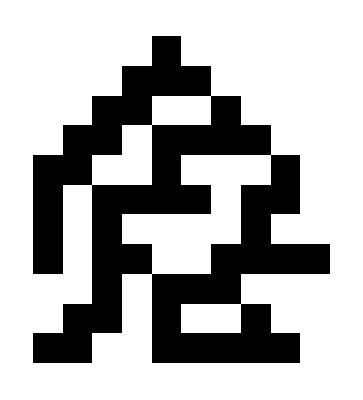
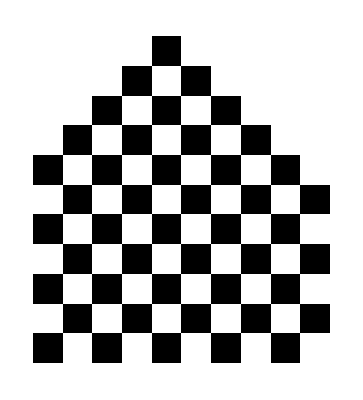
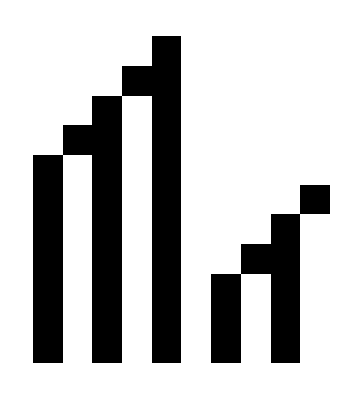

```mathematica
ArrayPlot/@cas
```

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[{30,50}],{init},3,"StatesGraph"]
```

-Graphics-

```mathematica
multi[CellularAutomaton[{30,50}],{init},1]
```

{{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0}}}

```mathematica
CellularAutomaton[30,init,1]
```

{{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,1,1,0,0,0,0}}

```mathematica
CellularAutomaton[50,init,1]
```

{{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0}}

```mathematica
multi[CellularAutomaton/@{30,50},{init},1]
```

{{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0}}}

```mathematica
multi[CellularAutomaton[30],{init},1]
```

{{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0}}}

```mathematica
multi[{CellularAutomaton[30]},{init},1]
```

{{{0,0,0,0,1,0,0,0,0,0}},{{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,0,0}}}

```mathematica
multi[{{CellularAutomaton[30df]}},{init},1]
```

[◼] | MultiwaySystem [{{CellularAutomaton[30]}},{{0,0,0,0,1,0,0,0,0,0}},1]

```mathematica
multi[ {"A"->"ABA","AA"->"B"},"AABAA",2]
```

{{AABAA},{AABAABA,AABABAA,AABB,ABAABAA,BBAA},{AABAABABA,AABABAABA,AABABABAA,AABABB,AABBBA,ABAABAABA,ABAABABAA,ABAABB,ABABAABAA,ABBBAA,BBAABA,BBABAA,BBB}}

```mathematica
multi[ {#->#/.{"A"->"ABA","AA"->"B"}&,#->#/.{"A"->"AA","B"->"BB"}&}"AABAA",2]
```

[◼] | MultiwaySystem [{AABAA (#1→#1/.{A→ABA,AA→B}&),AABAA (#1→#1/.{A→AA,B→BB}&)},2]

```mathematica
(#->#/.{"A"->"ABA","AA"->"B"}&)["AABAA"]
```

AABAA→AABAA